```mathematica
stokeslet[x_,e_]:= 3/40 (e+Dot[x,e]x/Norm[x]^2)/Norm[x];
dipole[x_,d_,e_]:= 3/40((Dot[x,d]e-Dot[e,x]d-Dot[d,e]x)/Norm[x]+(3Dot[e,x]Dot[d,x]x)/Norm[x]^3)/Norm[x]^2;
doublet[x_,e_]:=3/40(-e+3Dot[e,x]x/Norm[x]^2)/Norm[x]^3;blakelet[x_,y_,e_]:= stokeslet[x-y,e]+(-stokeslet[y-(x-{0,2 x[[2]]}),{1,0}] +2x[[2]]dipole[y-(x-{0,2 x[[2]]}),{1,0},{0,1}]-2x[[2]]^2 doublet[y-(x-{0,2 x[[2]]}),{1,0}])e[[1]] + (-stokeslet[y-(x-{0,2 x[[2]]}),{0,1}] +2x[[2]]dipole[y-(x-{0,2 x[[2]]}),{0,1},{0,1}]-2x[[2]]^2 doublet[y-(x-{0,2 x[[2]]}),{0,1}])e[[2]];
```

```mathematica
xx[t_]={Cos[t],Sin[t]+2};
```

```mathematica
xxdot[t_]=N[D[xx[t],t]];
```

```mathematica
f[y_,t_]=blakelet[xx[t],y,xxdot[t]];
f2[y1_,y2_,t_]=blakelet[xx[t],{y1,y2},xxdot[t]];
```

```mathematica
Animate[VectorPlot[f2[x1,x2,t],{x1,-2,2},{x2,0,3}],{t,0,2Pi}];
```

```mathematica
{y1,y2}=NDSolveValue[{{y1'[t],y2'[t]}==f2[y1[t],y2[t],t],y1[0]==0,y2[0]==0.5},{y1,y2},{t,0,2Pi}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

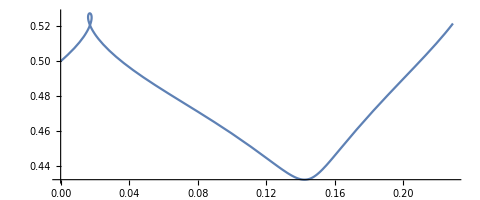

```mathematica
ParametricPlot[{y1[t],y2[t]},{t,0,2Pi}]
```

```mathematica
tracer=ParametricNDSolveValue[{{y11'[t],y22'[t]}==f2[y11[t],y22[t],t],y11[0]==b1,y22[0]==b2},{y11[2Pi]-y11[0],y22[2Pi]-y22[0]},{t,0,2Pi},{b1,b2}];
```

```mathematica
VectorPlot[tracer[p,q],{p,-2,2},{q,0,3}]
```

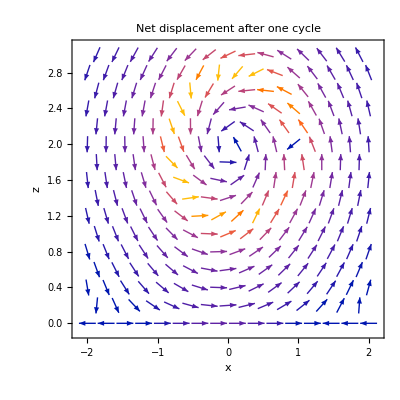

```mathematica
Show[%33,FrameLabel->{{HoldForm[z],None},{HoldForm[x],None}},PlotLabel->HoldForm[Net displacement after one cycle],LabelStyle->{FontFamily->"Calibri",12,GrayLevel[0]}]
```